# Calculating AVS Curves

## QEA Boats Module

By Dieter Brehm & Sam Sam Daitzman

## Explanation

### This file contains Mathematica code for calculating the RM curve of a differently shaped three dimensional boats. First, we define our desired boats. Then, we define a function for finding the moment at a given heal angle. Finally, we map that function to several angles and generate a plot.

## Code

Defining and showing a plot of the two boats

```mathematica
oldboat = ImplicitRegion[x^2/2<y<2 && -2 < x<2&&0<y<2 && -5 < z <5, {x,y,z}]
```

ImplicitRegion[x^2/2<y<2&&-2<x<2&&0<y<2&&-5<z<5,{x,y,z}]

```mathematica
RegionPlot3D[oldboat, PlotTheme->"Web", AxesLabel->{"x","y","z"}, PlotPoints->55, PlotStyle->Directive[Yellow,Opacity[0.5]]]
```

```mathematica
boat = ImplicitRegion[(x)^2/(10.16)^2+(y-15.24)^2/(15.24)^2 +z^2/(20.32)^2<1 && y < 15.24,{ {x,-20,20},{y,-20,20},{z,-50,50}}];
```

```mathematica
Show[
RegionPlot3D[boat, PlotTheme->"Web", AxesLabel->{"x","y","z"}, PlotPoints->55, PlotStyle->Directive[Yellow,Opacity[0.5]]],
ListPointPlot3D[{{0,0.751588,0}}, PlotStyle->Directive[Cyan,Opacity[1]]]]
```

-Graphics3D-

Code for calculating moment of arbitrary ImplicitRegion boat at a heel angle

```mathematica
boatmass[boatregion_, density_] :=
 mass = N[(Volume[boatregion]*density)+800.,5]
boatcom[boatregion_, density_] := 
com = N[ 1/(boatmass[boatregion, density]+800.)*NIntegrate[density*{x,y,z}, {x,y,z}∈boatregion],5]
moment[hullshape_,mass_,com_,density_, theta_]:= Module[{},
rads = theta * (Pi/180);
water = ImplicitRegion[If[rads<Pi / 2,y<Tan[rads ]*x+d,y>Tan[rads]*x+d],{{x,-2,2},{y,-2,2}, {z,-5,5}}];
under = RegionIntersection[hullshape, water];
disp = Integrate[1000, {x,y,z}∈under];
draft = N[d/.FindRoot[disp==mass,{d,-20,20}][[1]]];
cob = RegionCentroid[under/.{d->draft}];
buoyancy = mass*98/10*{-Sin[rads],Cos[rads],0};
torque =Cross[cob-com, buoyancy][[3]];
torque
]
```

```mathematica
moment[oldboat,boatmass[oldboat, 300.],boatcom[oldboat,300.],300.,30.]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

91518.2

Testing intermediary functions and plots

```mathematica
ListPlot[Parallelize[Table[{N[theta,1],moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,N[theta,1]]},{theta,{0.,10.,20.,30.,40.,50.,60.,70.,80.,100.,110.,120.,130.,140.,150.,160.,170.,180.}}]]]
```

Attempted mapping of angles to moment outputs

I can’t seem to get this to run reasonably. It takes much longer for this to run (I havn’t run it long enough for it to finish because it is taking so long} than just manually running the function and entering plot points.

```mathematica
boatmass[boat, 300.]
boatcom[boat,300.]
boatmass[oldboat, 300.]
boatcom[oldboat,300.]
```

10053.1

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{0.,1.25,0.}

16000.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{0.,1.2,0.}

```mathematica
f[anAngle_] := moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,anAngle]
rmcurve[boat_] := N[Quiet[Parallelize[Table[{angle,N[f[angle]]},{angle,1,179,179}]]]]
findAVS[boat_]:= (
f = Interpolation[rmcurve[boat]];
FindRoot[f[x]==0,{x,100}])
PlotAVS[boat_]:=(
curves = N[Quiet[Parallelize[Table[{angle,N[f[angle]]},{angle,1,179,179}]]]];
f = Interpolation[curves];
Print[Show[ListPlot[curves],Plot[f[x],{x,1,179}]]])
plotAVS[oldboat]
```

manual runs of data for ellipse boat

```mathematica
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,10.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,20.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,30.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,40.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,50.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,60.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,70.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,80.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,100.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,120.]
```

```mathematica
a={}
For[i=1,i<180,i+=20, Print[i];a =Append[a,moment[boat,boatmass[boat, 0.01],boatcom[boat,0.01],300.,N[i,1]]]]
```

{}

1

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

21

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

41

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

61

81

101

121

141

161

```mathematica
a
```

{962.26,12082.9,11797.8,8896.4,8177.19,7799.66,2325.19,-4106.12,-9528.09}

```mathematica
b = {1,21,41,61,81,101,121,141,161}
```

{1,21,41,61,81,101,121,141,161}

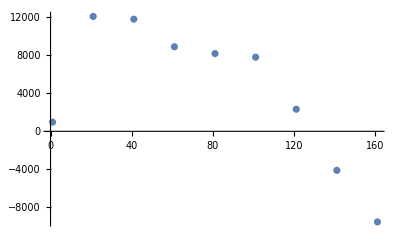

```mathematica
data=Transpose@{b,a};
ListPlot[data]
```

```mathematica
f=Interpolation[data]
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {0.00367714} lies outside the range of data in the interpolating function. Extrapolation will be used.

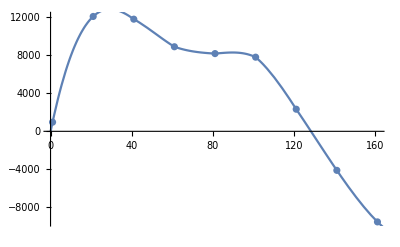

```mathematica
Show[
ListPlot[data],Plot[f[x],{x,0,180}]]
```

```mathematica
FindRoot[f[x]==0,{x,100}]
```

InterpolatingFunction::dmval: Input value {189.126} lies outside the range of data in the interpolating function. Extrapolation will be used.

{x→128.254}

```mathematica
For[i=3,i<180,i+=2, Print[i]]
```

```mathematica
f = Interpolation[exampledata]
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {0.00367714} lies outside the range of data in the interpolating function. Extrapolation will be used.

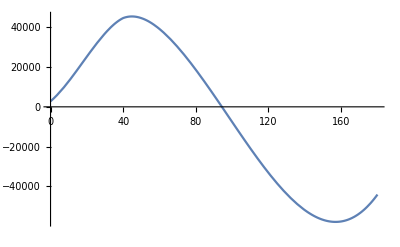

```mathematica
Plot[f[x],{x,0,180}]
```

```mathematica
FindRoot[f[x]==0,{x,100}]
```

{x→67.6027}